100

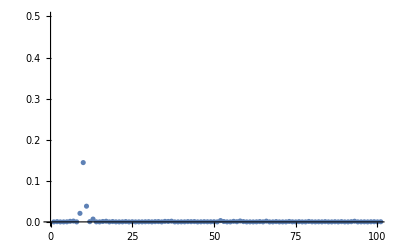

```mathematica
n=100
SinSteps = Table[Sin[2π (10x+0.2RandomReal[])],{x,Range[0,0.5,0.5/n]}];
ListPlot[FourierDST[SinSteps]^2/n,PlotRange->{{0,n},{0,0.5}}]
```